```mathematica
Needs["DeepZot`CosmoTools`"]
```

```mathematica
createCosmology[Planck13]
```

```mathematica
SetDirectory["/Users/david/Cosmo/DESC/DarkEnergySchool/LargeScaleStructureStatistics/camb/"]
```

/Users/david/Cosmo/DESC/DarkEnergySchool/LargeScaleStructureStatistics/camb

```mathematica
exportToCamb["Planck13.camb",Planck13,redshifts->{0,1.2}]
```

Planck13.camb

```mathematica
Needs["DeepZot`PowerTools`"]
```

```mathematica
Pk=makePower[ReadList["Planck13_matterpower_1.dat",Number,RecordLists->True]];
```

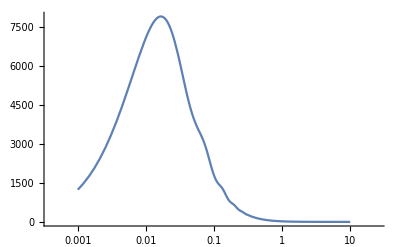

```mathematica
LogLinearPlot[Pk[k],{k,0.001,10}]
```

```mathematica
?comovingDistanceFunction
```

comovingDistanceFunction[cosmology,zmax] returns a function that evaluates the comoving distance
along the line of sight to a redshift z <= zmax for the named cosmology. Possible options (with
defaults in parentheses) are:
 - physical (False) units are Mpc (True) or Mpc/h (False).
 - inverted (False) return inverse function z(Dc) instead of Dc(z) when True.
 - pointsPerDecade (20) number of interpolation points to use per decade.

```mathematica
Dc=comovingDistanceFunction[Planck13,2,physical->True];
```

```mathematica
Dc[1]
```

3412.7